```mathematica
Series[1/(ⅈ ω Q Sqrt[C/L]+Q^2/R^2 L-ω^2 Q^4 C^2/R^4),{Q,0,1}]
```

-ⅈ/(√(C/L) ω Q)+L^2/(C R^2 ω^2)+(ⅈ L^3 Q)/(C √(C/L) R^4 ω^3)+O[Q]^2

```mathematica
Series[1/(ⅈ ω Q Sqrt[C/L]+Q^2/R^2 L-ω^2 Q^4 C^2/R^4),{Q,Infinity,4}]
```

-R^4/(C^2 ω^2 Q^4)+O[1/Q]^5

```mathematica
R1=400;C1=4;L1=16;
```

```mathematica
R2=1;L2=1;C2=1;
```

```mathematica
R3=25;C3=4;L3=16;
```

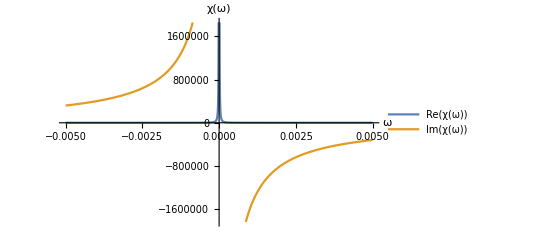

```mathematica
Plot[{L1^2/(C1 R1^2 ω^2),L1^4/(ω^3 R1^5 C1^2)-(L1 R1)/(ω C1)}, {ω,-0.005,0.005},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

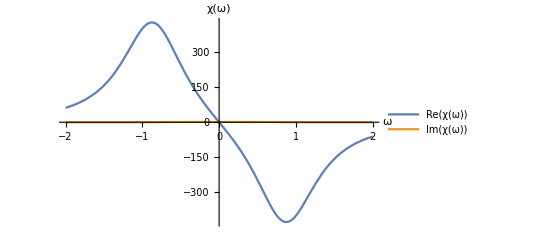

```mathematica
Plot[{-(ω R1)/((-ω^2 L2^2+1/C2)^2+ω^2 R2^2),(-ω^2 L2^2+1/C2)/((-ω^2 L2^2+1/C2)^2+ω^2 R2^2)}, {ω,-2,2},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

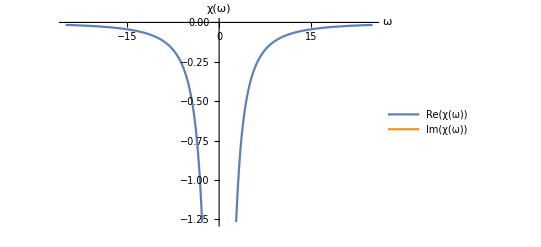

```mathematica
Plot[{-R3^2/(ω^2 L3 C3),None}, {ω,-25,25},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

```mathematica
Solve[ⅈ ω R-ω^2 L^2+1/C==0,ω]
```

{{ω→-(-ⅈ R-(√(4 L^2-C R^2))/(√C))/(2 L^2)},{ω→-(-ⅈ R+(√(4 L^2-C R^2))/(√C))/(2 L^2)}}

```mathematica
ωp=1/10; τ=100;
```

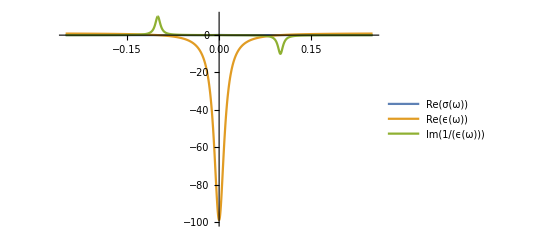

```mathematica
Plot[{ωp^2/(4Pi τ)1/(1/τ^2+ω^2),1-ωp^2/(1/τ^2+ω^2),-ω/τ ωp^2/((ω^2-ωp^2)^2+ω^2/τ^2)},{ω,-0.25,0.25},PlotLegends->{Re[σ[ω]],Re[ϵ[ω]],Im[1/ϵ[ω]]},PlotRange->{-100,10},Ticks->{None}]
```

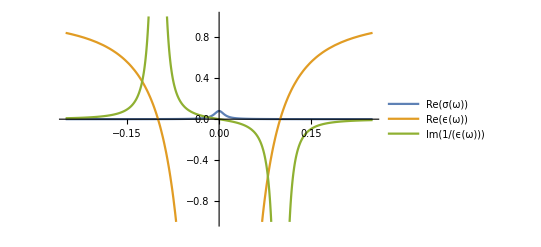

```mathematica
Plot[{ωp^2/(4Pi τ)1/(1/τ^2+ω^2),1-ωp^2/(1/τ^2+ω^2),-ω/τ ωp^2/((ω^2-ωp^2)^2+ω^2/τ^2)},{ω,-0.25,0.25},PlotLegends->{Re[σ[ω]],Re[ϵ[ω]],Im[1/ϵ[ω]]},PlotRange->{-1,1},Ticks->{None}]
```

```mathematica
Series[1/(1/x^2+1),{x,0,2}]
```

x^2+O[x]^3

```mathematica
Series[2-2Sqrt[1-A x^2]-A b x^2,{x,0,2}]
```

(A-A b) x^2+O[x]^3

```mathematica
Series[2+2Sqrt[1-A x^2]-A b x^2,{x,0,2}]
```

4+(-A-A b) x^2+O[x]^3

```mathematica
Series[1-2Sqrt[K /x],{x,0,2}]
```

-(2 (√(K/x) √x))/(√x)+1+O[x]^(5/2)

```mathematica
Series[(-γ ω)/((K q^2-ρ ω^2)^2+γ^2 ω^2),{γ,0,2}]
```

-(ω γ)/((K q^2-ρ ω^2)^2)+O[γ]^3

```mathematica
Apart[(γ ωr)/((ωr-ω)(K q^2-ρ ωr^2)^2)]
```

(γ ω)/((K q^2-ρ ω^2)^2 (-ω+ωr))+(K q^2 γ+γ ρ ω ωr)/((K q^2-ρ ω^2) (-K q^2+ρ ωr^2)^2)+(-γ ρ ω^2-γ ρ ω ωr)/((K q^2-ρ ω^2)^2 (-K q^2+ρ ωr^2))

```mathematica
Integrate[1/(-ω+ωr),{ωr,-Infinity, Infinity},Assumptions->{ω∈Reals,ϵ>0},PrincipalValue->True]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

Integrate::idiv: Integral of 1/(-ω+ωr) does not converge on {-∞,∞}.

Integrate[1/(-ω+ωr),{ωr,-∞,∞},Assumptions→{ω∈ℝ,ϵ>0},PrincipalValue→True]

```mathematica
Integrate[1/x,{x,-Infinity,-ϵ}]
```

Integrate::idiv: Integral of 1/x does not converge on {-∞,-ϵ}.

∫_(-∞)^-ϵ 1/x ⅆx

```mathematica
Limit[(γ ω Log[(-R+ω)/(R+ω)])/((K q^2-ρ ω^2)^2),R->Infinity]
```

(ⅈ π γ ω)/((K q^2-ρ ω^2)^2)

```mathematica
Integrate[(K q^2 γ+γ ρ ω ωr)/((K q^2-ρ ω^2) (-K q^2+ρ ωr^2)^2),{ωr,-R, R},Assumptions->{ω∈Reals,γ∈Reals,K∈Reals,q∈Reals,ρ∈Reals,R∈Reals,R>0}]
```

(γ ((q R)/(K q^2-R^2 ρ)+ArcTanh[(R √ρ)/(√K q)]/(√K √ρ)) Sign[q]^2)/(K q^3-q ρ ω^2)

```mathematica
Limit[(γ ((q R)/(K q^2-R^2 ρ)+ArcTanh[(R √ρ)/(√K q)]/(√K √ρ)))/(K q^3-q ρ ω^2),R->Infinity]
```

-(π γ √(-ρ/(K q^2)))/(2 K q^2 ρ-2 ρ^2 ω^2)

```mathematica
Integrate[(-γ ρ ω^2-γ ρ ω ωr)/((K q^2-ρ ω^2)^2 (-K q^2+ρ ωr^2)),{ωr,-R, R},Assumptions->{ω∈Reals,γ∈Reals,K∈Reals,q∈Reals,ρ∈Reals,R∈Reals,R>0}]
```

(2 γ √ρ ω^2 ArcTanh[(R √ρ)/(√K q)])/(√K q (K q^2-ρ ω^2)^2)

```mathematica
Limit[(2 γ √ρ ω^2 ArcTanh[(R √ρ)/(√K q)])/(√K q (K q^2-ρ ω^2)^2),R->Infinity]
```

-(π γ √(-ρ/(K q^2)) ω^2)/((K q^2-ρ ω^2)^2)

```mathematica
Simplify[-(π γ √(-ρ/(K q^2)))/(2 K q^2 ρ-2 ρ^2 ω^2)-(π γ √(-ρ/(K q^2)) ω^2)/((K q^2-ρ ω^2)^2)]
```

-(π γ √(-ρ/(K q^2)) (K q^2+ρ ω^2))/(2 ρ (K q^2-ρ ω^2)^2)

```mathematica
Clear[P]
```

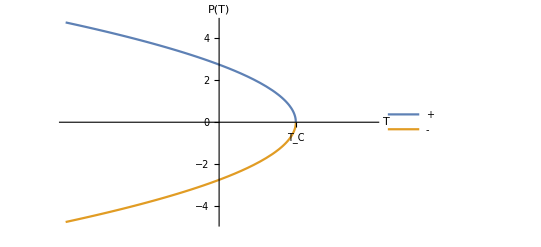

```mathematica
Plot[{Sqrt[3/2(5-t)],-Sqrt[3/2(5-t)]},{t,-10,10},PlotLegends->{"+","-"},Ticks->{{{5,Subscript[T, C]}},{None}},AxesLabel->{T,P[T]}]
```

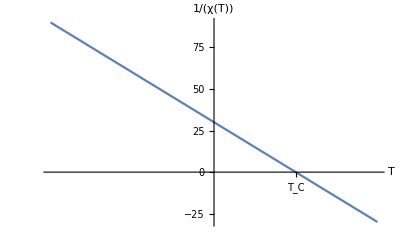

```mathematica
Plot[6(5-t),{t,-10,10},Ticks->{{{5,Subscript[T, C]}},{None}},AxesLabel->{T,1/χ[T]}]
```

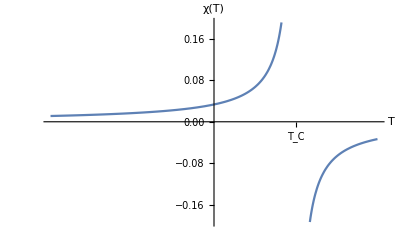

```mathematica
Plot[1/(6(5-t)),{t,-10,10},Ticks->{{{5,Subscript[T, C]}},{None}},AxesLabel->{T,χ[T]}]
```

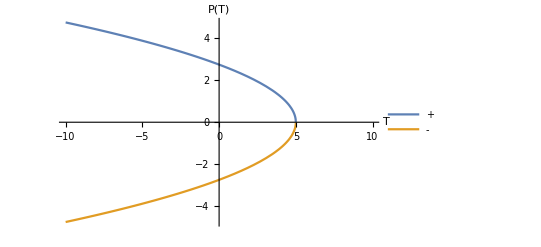

```mathematica
Plot[{√((3 (5-t))/2),-√((3 (5-t))/2)},{t,-10,10},PlotLegends->{"+","-"},
Ticks->{None},AxesLabel->{T,P[T]}]
```

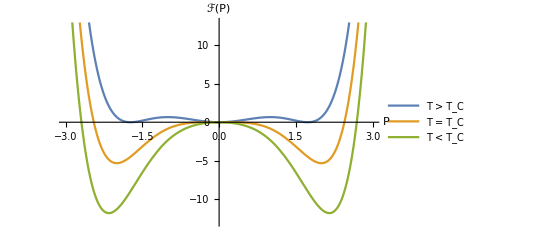

```mathematica
Plot[{3/2 p^2-p^4+1/6 p^6,-p^4+1/6 p^6,-3/2 p^2-p^4+1/6 p^6},{p,-3,3},PlotRange->{-13,13},PlotLegends->{"T > T_C","T = T_C","T < T_C"},AxesLabel->{P,ℱ[P]},Ticks->{None}]
```

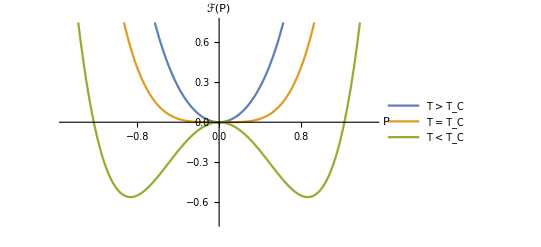

```mathematica
Plot[{3/2 p^2+p^4,p^4,-3/2 p^2+p^4},{p,-1.5,1.5},PlotRange->{-0.75,0.75},PlotLegends->{"T > T_C","T = T_C","T < T_C"},AxesLabel->{P,ℱ[P]},Ticks->{None}]
```

```mathematica
Series[A/(x+ⅈ),{x,0,1}]
```

-ⅈ A+A x+O[x]^2

```mathematica
Simplify[(1-2x+2 x^2)/(1+2x+2 x^2)]
```

(1-2 x+2 x^2)/(1+2 x+2 x^2)

```mathematica
Series[(1-2Sqrt[x]+x)/(1+2Sqrt[x]+x),{x,Infinity,2}]
```

1-4 √(1/x)+8/x-12 (1/x)^(3/2)+16/x^2+O[1/x]^(5/2)

```mathematica
Series[(1+x)^(1/4),{x,0,1}]
```

1+x/4+O[x]^2